```mathematica
ArrayPlot/@CellularAutomaton[{120,{3,{{0,1,0,1,0},{0,1,1,1,1},{1,1,1,1,0},{0,0,1,0,0},{0,0,0,1,0}}},{2,2}},{{{1}},0},20]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

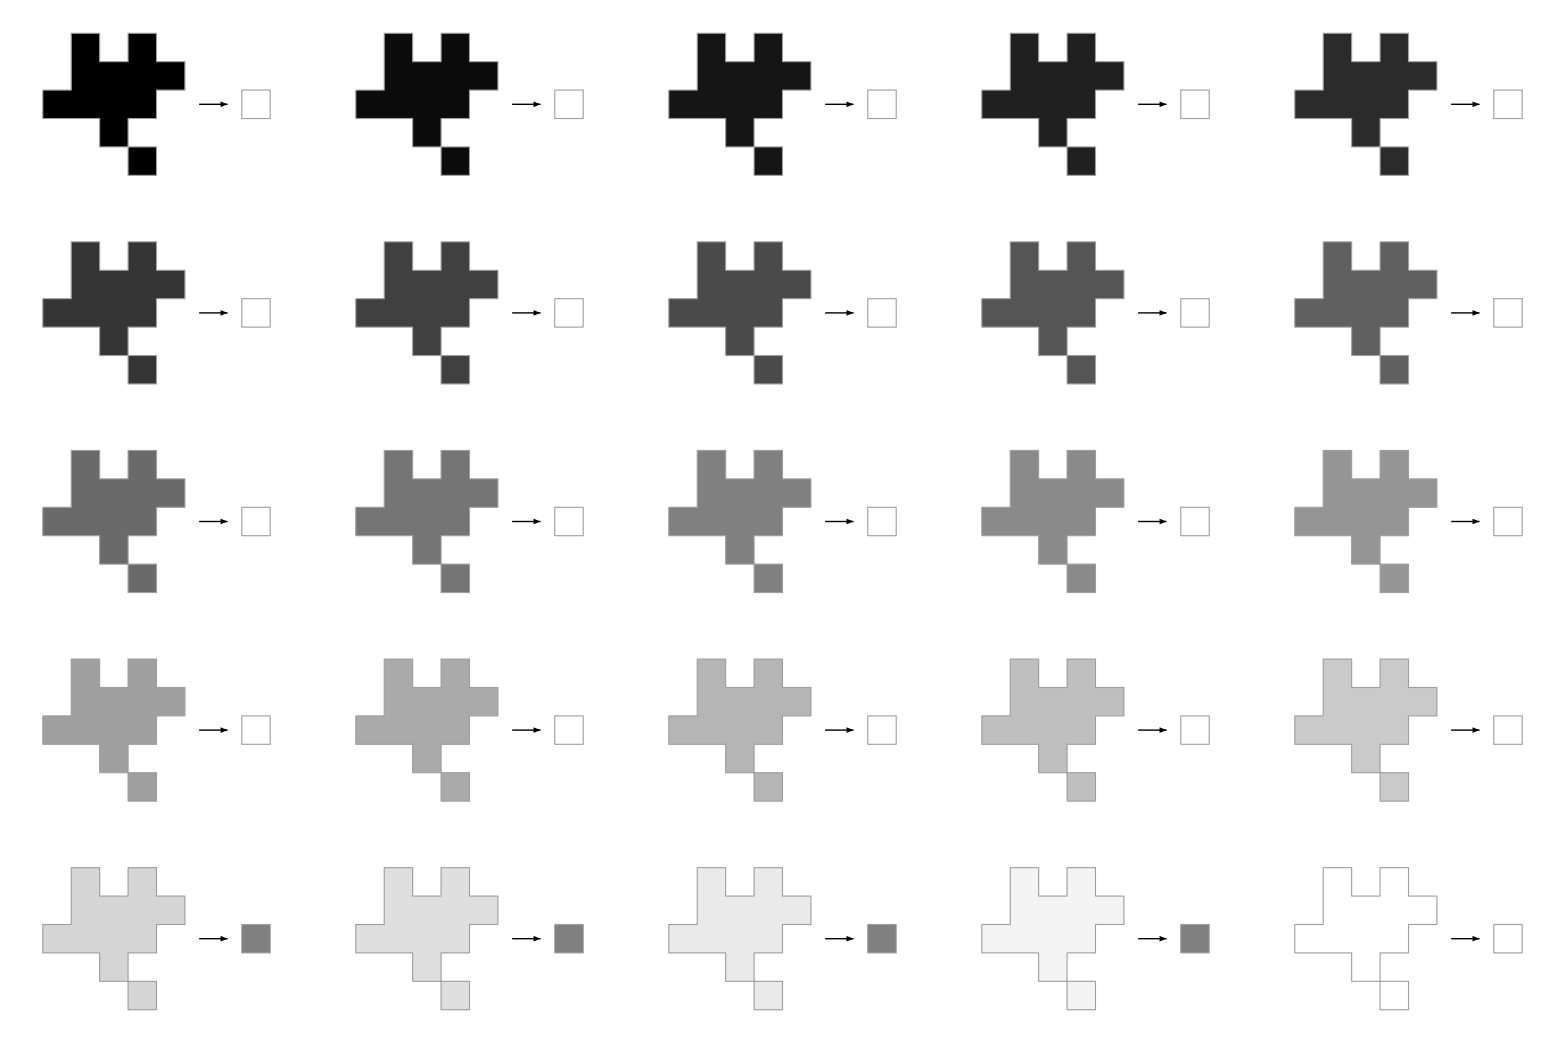

```mathematica
RulePlot[CellularAutomaton[{120,{3,{{0,1,0,1,0},{0,1,1,1,1},{1,1,1,1,0},{0,0,1,0,0},{0,0,0,1,0}}},{2,2}}]]
```

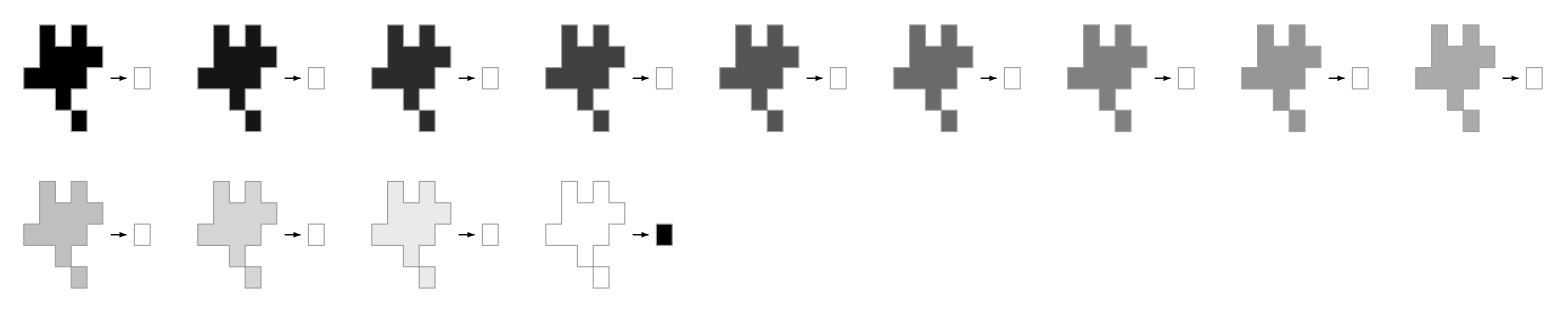

```mathematica
RulePlot[CellularAutomaton[{1,{2,{{0,1,0,1,0},{0,1,1,1,1},{1,1,1,1,0},{0,0,1,0,0},{0,0,0,1,0}}},{2,2}}]]
```

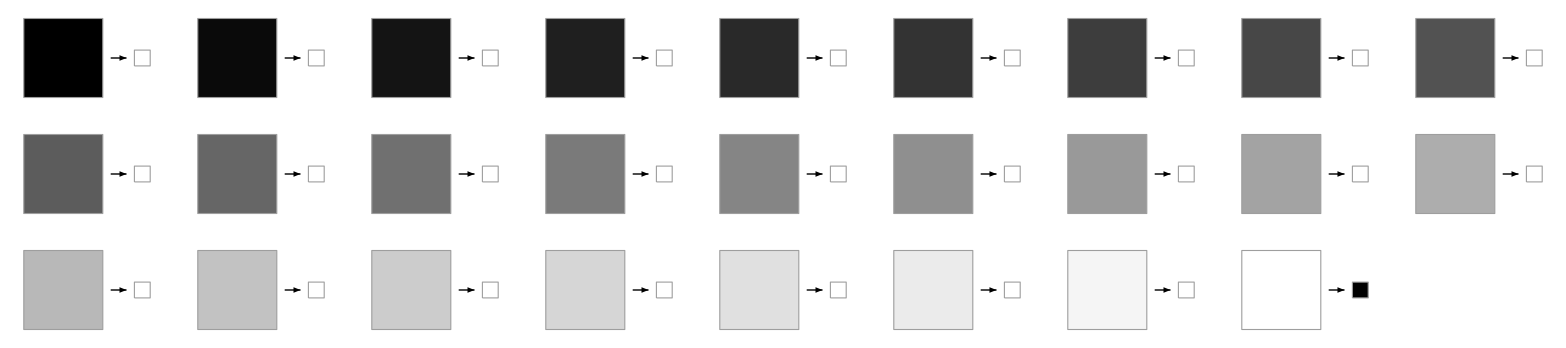

```mathematica
RulePlot[CellularAutomaton[{1,{2,1},{2,2}}]]
```

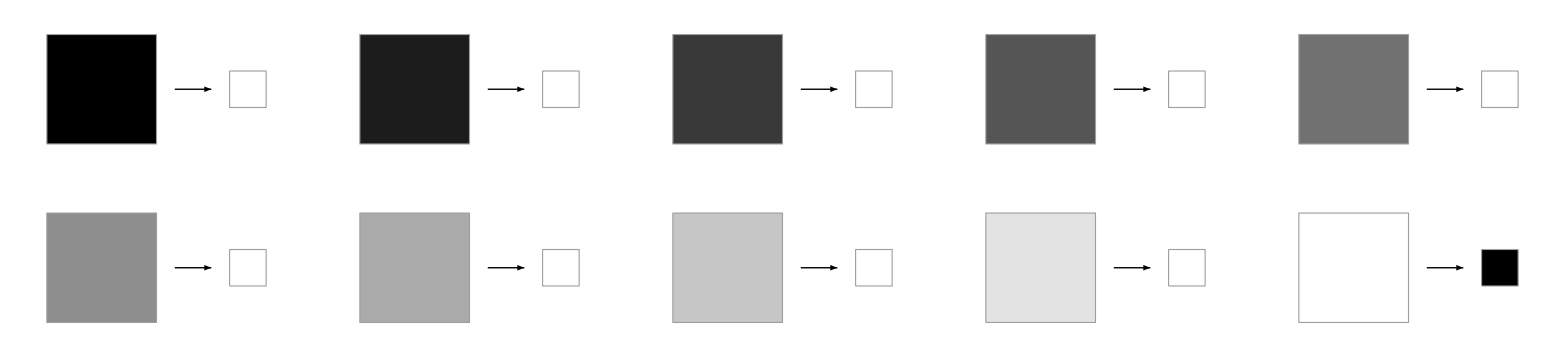

```mathematica
RulePlot[CellularAutomaton[{1,{2,1},{1,1}}]]
```

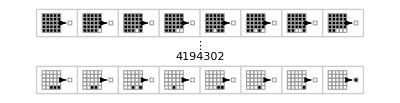

```mathematica
RulePlot[CellularAutomaton[{1,2,{2,2}}]]
```

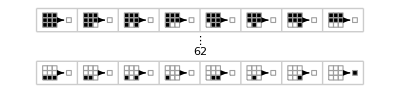

```mathematica
RulePlot[CellularAutomaton[{1,2,{1,1}}]]
```

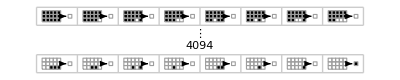

```mathematica
RulePlot[CellularAutomaton[{1,2,{1,2}}]]
```

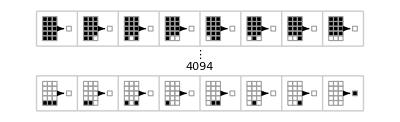

```mathematica
RulePlot[CellularAutomaton[{1,2,{2,1}}]]
```

```mathematica
2^(2^25)
```

3307252488173983134055805191972697547112915208119555897061135336548567034515118156741405454858318041647791899238204314297627488851800420985897375410100598333305370921626727509897477048225888177635909407102228767954290067571974851216058292917894686139157068577362825588529512324229490098788901161271296
 |  |  |  |

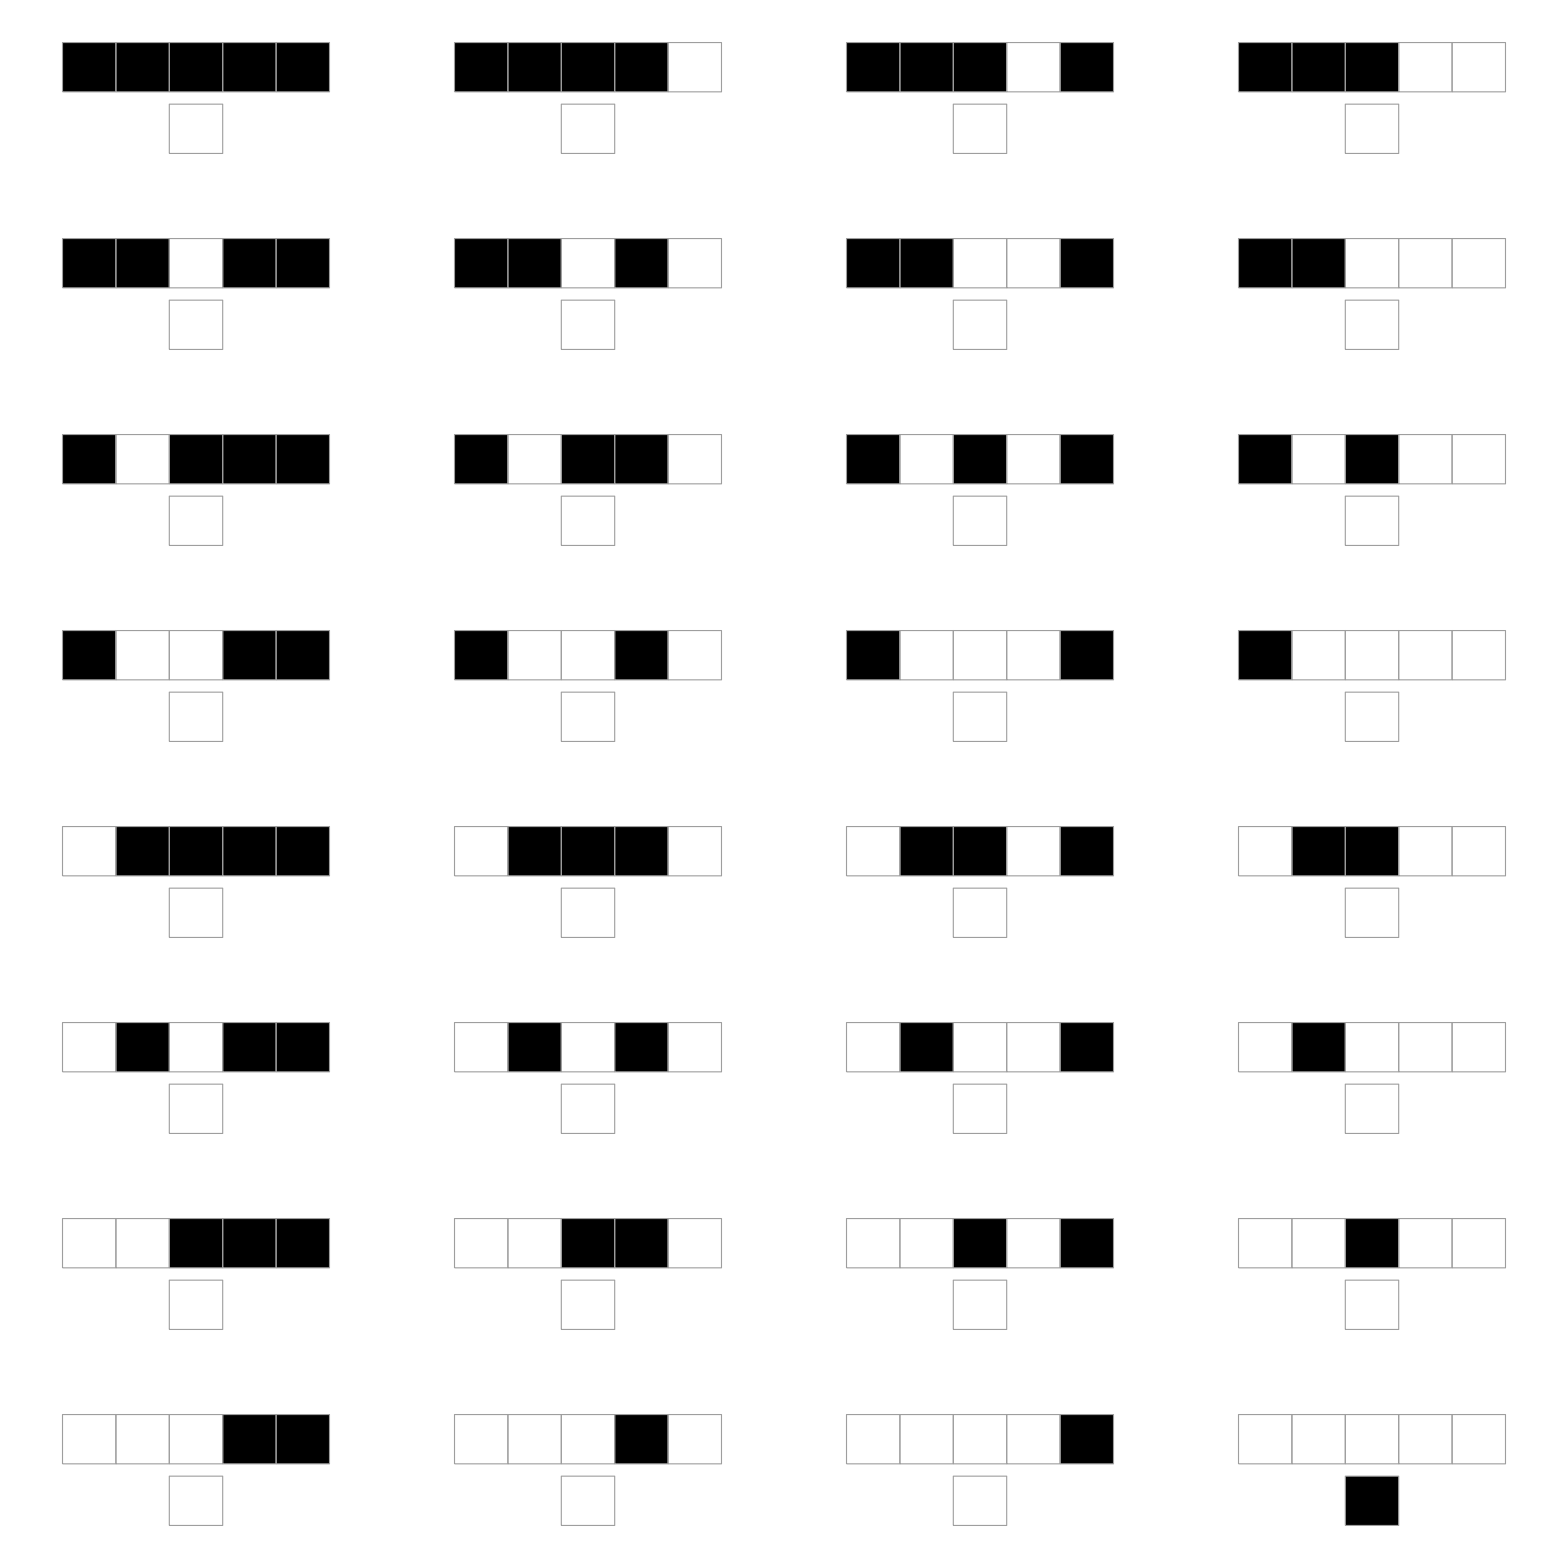

```mathematica
RulePlot[CellularAutomaton[{1,2,2}]]
```

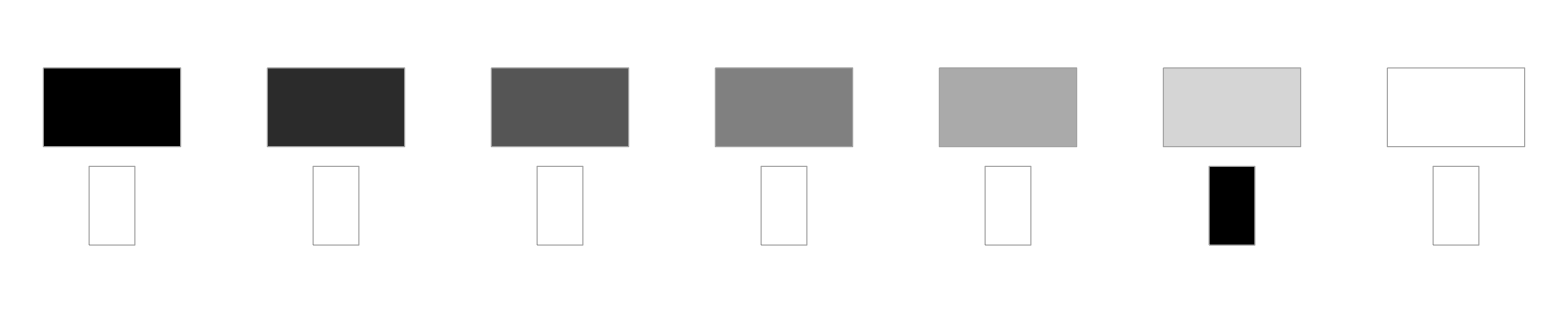

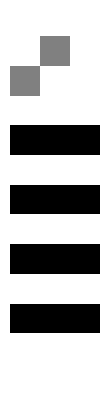

```mathematica
RulePlot[CellularAutomaton[{ruleNumber,{3,1},1}]]
ArrayPlot@CellularAutomaton[{ruleNumber,4,1},{{1},0},10]
```

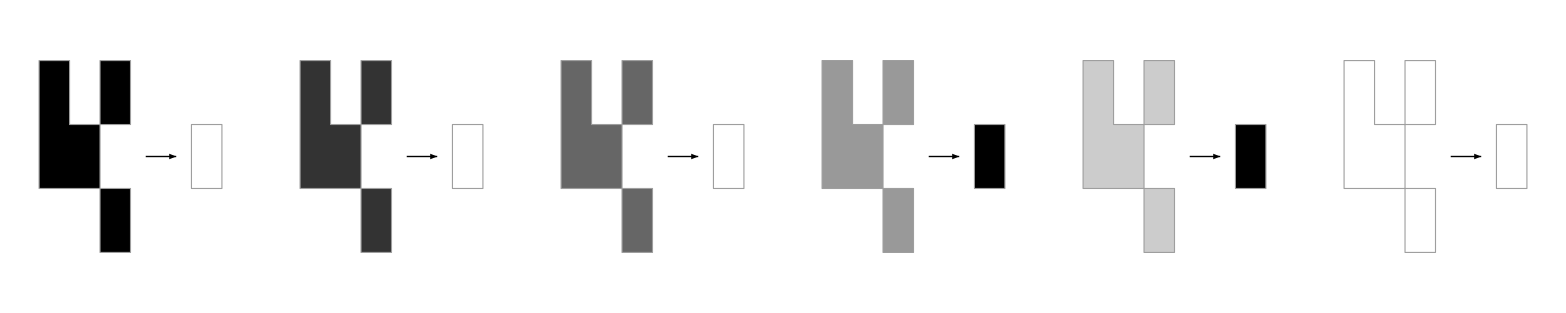

-Graphics-

```mathematica
ruleNumber=6;
RulePlot[CellularAutomaton[{ruleNumber,{2,{{1,0,1},{1,1,0},{0,0,1}}},{1,1}}]]
ArrayPlot[Last[#]]&@CellularAutomaton[{ruleNumber,{2,{{1,0,1},{1,1,0},{0,0,1}}},{1,1}},{{{1}},0},200]
```

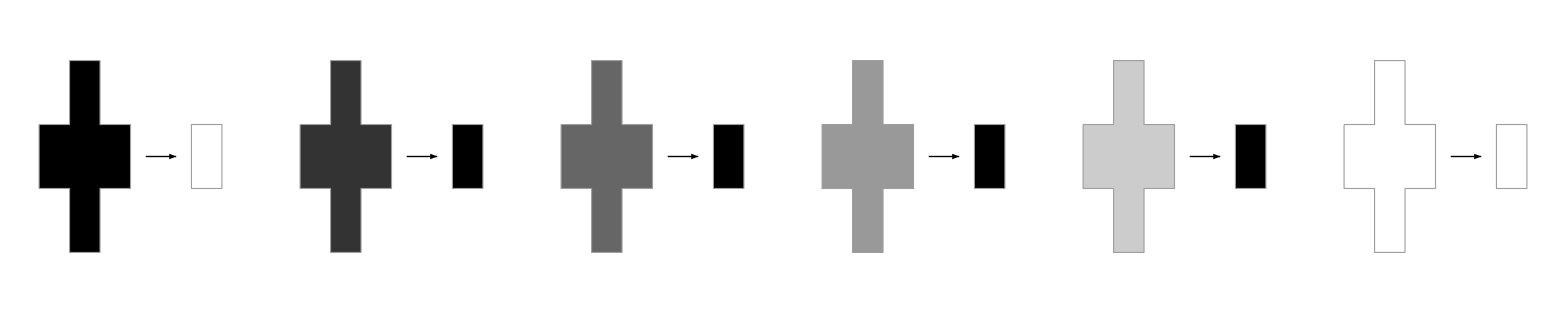

```mathematica
RulePlot[CellularAutomaton[{30,{2,{{0,1,0},{1,1,1},{0,1,0}}},{1,1}}]]
```

```mathematica
{{Table[1,7]},0}
```

{{{1,1,1,1,1,1,1}},0}

```mathematica
{{{150}}}
```

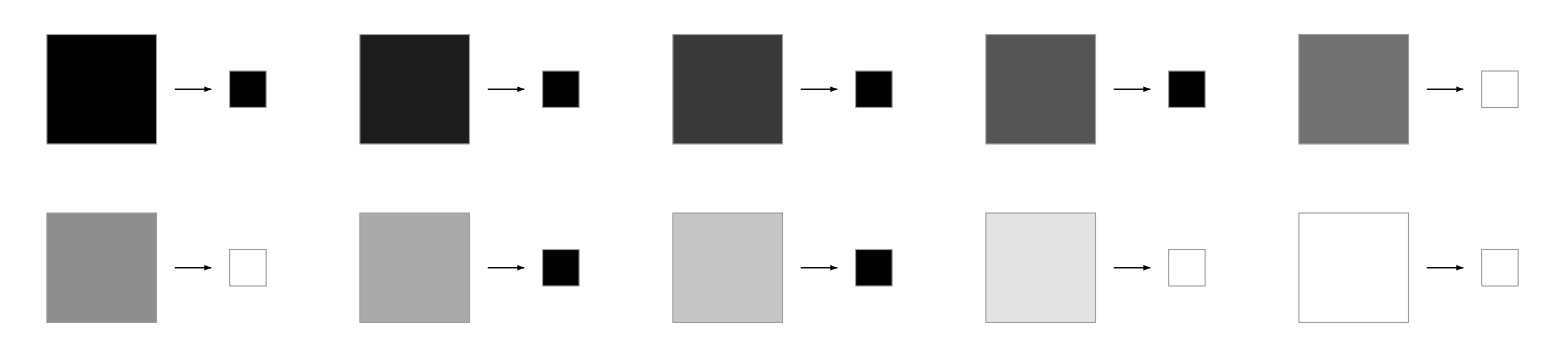

```mathematica
RulePlot[CellularAutomaton[{972,{2,1},{1,1}}]]
```

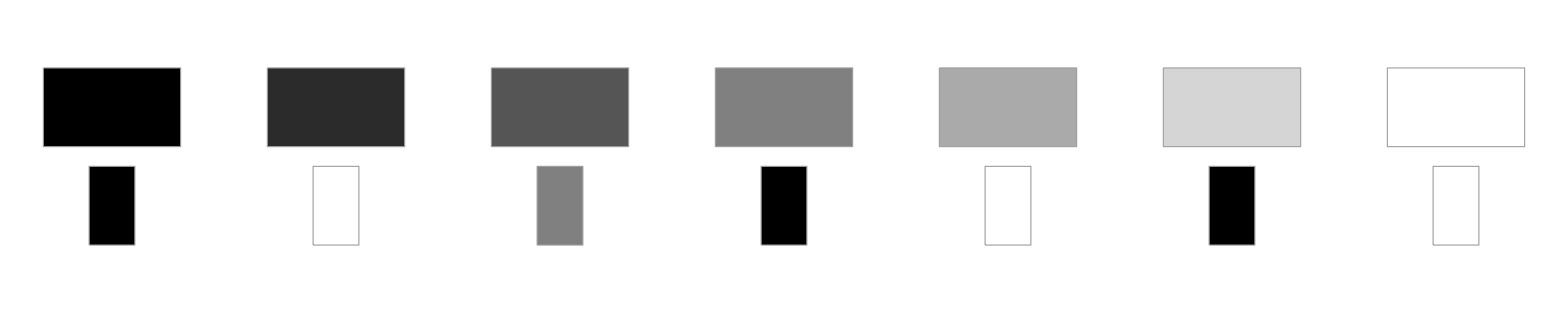

```mathematica
RulePlot[CellularAutomaton[{1599,{3,1}}]]
```

```mathematica
ArrayPlot[CellularAutomaton[{1599,{3,1}},{{1},0},500]]
```

-Graphics-

```mathematica
RulePlot[CellularAutomaton[{30,{3,1},{2,2,2}}]]
```

RulePlot[CellularAutomaton[{30,{3,1},{2,2,2}}]]

```mathematica
{{1},0}
```

{{1},0}

```mathematica
SubstitutionSystem[{1->{1,0},0->0}]
```

SubstitutionSystem[{1→{1,0},0→0}]

```mathematica
{1}
```

```mathematica
FromDigits[#,2]&/@SubstitutionSystem[{1->{1,0}},{1,1},10]
```

{3,10,36,136,528,2080,8256,32896,131328,524800,2098176}

```mathematica
SubstitutionSystem[{1->{1,0}},{1},10]
```

{{1},{1,0},{1,0,0},{1,0,0,0},{1,0,0,0,0},{1,0,0,0,0,0},{1,0,0,0,0,0,0},{1,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0}}

```mathematica
Column[ArrayPlot[{#}]&/@SubstitutionSystem[{1->{1,0},0->0},{1},10]]
```

-Graphics-

```mathematica
FromDigits[#,2]&/@SubstitutionSystem[{1->{1,0}},{1},10]
```

{1,2,4,8,16,32,64,128,256,512,1024}

```mathematica
FromDigits[{1,0,0,1},2]+FromDigits[{1,0,1,0},2]
```

19

```mathematica
Range[100]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

```mathematica
PadLeft[#,7]&/@(IntegerDigits[#,2]&/@Range[100])
```

{{0,0,0,0,0,0,1},{0,0,0,0,0,1,0},{0,0,0,0,0,1,1},{0,0,0,0,1,0,0},{0,0,0,0,1,0,1},{0,0,0,0,1,1,0},{0,0,0,0,1,1,1},{0,0,0,1,0,0,0},{0,0,0,1,0,0,1},{0,0,0,1,0,1,0},{0,0,0,1,0,1,1},{0,0,0,1,1,0,0},{0,0,0,1,1,0,1},{0,0,0,1,1,1,0},{0,0,0,1,1,1,1},{0,0,1,0,0,0,0},{0,0,1,0,0,0,1},{0,0,1,0,0,1,0},{0,0,1,0,0,1,1},{0,0,1,0,1,0,0},{0,0,1,0,1,0,1},{0,0,1,0,1,1,0},{0,0,1,0,1,1,1},{0,0,1,1,0,0,0},{0,0,1,1,0,0,1},{0,0,1,1,0,1,0},{0,0,1,1,0,1,1},{0,0,1,1,1,0,0},{0,0,1,1,1,0,1},{0,0,1,1,1,1,0},{0,0,1,1,1,1,1},{0,1,0,0,0,0,0},{0,1,0,0,0,0,1},{0,1,0,0,0,1,0},{0,1,0,0,0,1,1},{0,1,0,0,1,0,0},{0,1,0,0,1,0,1},{0,1,0,0,1,1,0},{0,1,0,0,1,1,1},{0,1,0,1,0,0,0},{0,1,0,1,0,0,1},{0,1,0,1,0,1,0},{0,1,0,1,0,1,1},{0,1,0,1,1,0,0},{0,1,0,1,1,0,1},{0,1,0,1,1,1,0},{0,1,0,1,1,1,1},{0,1,1,0,0,0,0},{0,1,1,0,0,0,1},{0,1,1,0,0,1,0},{0,1,1,0,0,1,1},{0,1,1,0,1,0,0},{0,1,1,0,1,0,1},{0,1,1,0,1,1,0},{0,1,1,0,1,1,1},{0,1,1,1,0,0,0},{0,1,1,1,0,0,1},{0,1,1,1,0,1,0},{0,1,1,1,0,1,1},{0,1,1,1,1,0,0},{0,1,1,1,1,0,1},{0,1,1,1,1,1,0},{0,1,1,1,1,1,1},{1,0,0,0,0,0,0},{1,0,0,0,0,0,1},{1,0,0,0,0,1,0},{1,0,0,0,0,1,1},{1,0,0,0,1,0,0},{1,0,0,0,1,0,1},{1,0,0,0,1,1,0},{1,0,0,0,1,1,1},{1,0,0,1,0,0,0},{1,0,0,1,0,0,1},{1,0,0,1,0,1,0},{1,0,0,1,0,1,1},{1,0,0,1,1,0,0},{1,0,0,1,1,0,1},{1,0,0,1,1,1,0},{1,0,0,1,1,1,1},{1,0,1,0,0,0,0},{1,0,1,0,0,0,1},{1,0,1,0,0,1,0},{1,0,1,0,0,1,1},{1,0,1,0,1,0,0},{1,0,1,0,1,0,1},{1,0,1,0,1,1,0},{1,0,1,0,1,1,1},{1,0,1,1,0,0,0},{1,0,1,1,0,0,1},{1,0,1,1,0,1,0},{1,0,1,1,0,1,1},{1,0,1,1,1,0,0},{1,0,1,1,1,0,1},{1,0,1,1,1,1,0},{1,0,1,1,1,1,1},{1,1,0,0,0,0,0},{1,1,0,0,0,0,1},{1,1,0,0,0,1,0},{1,1,0,0,0,1,1},{1,1,0,0,1,0,0}}

```mathematica
ArrayPlot[PadLeft[#,7]&/@(IntegerDigits[#,2]&/@Range[100]),Mesh->All]
```

-Graphics-

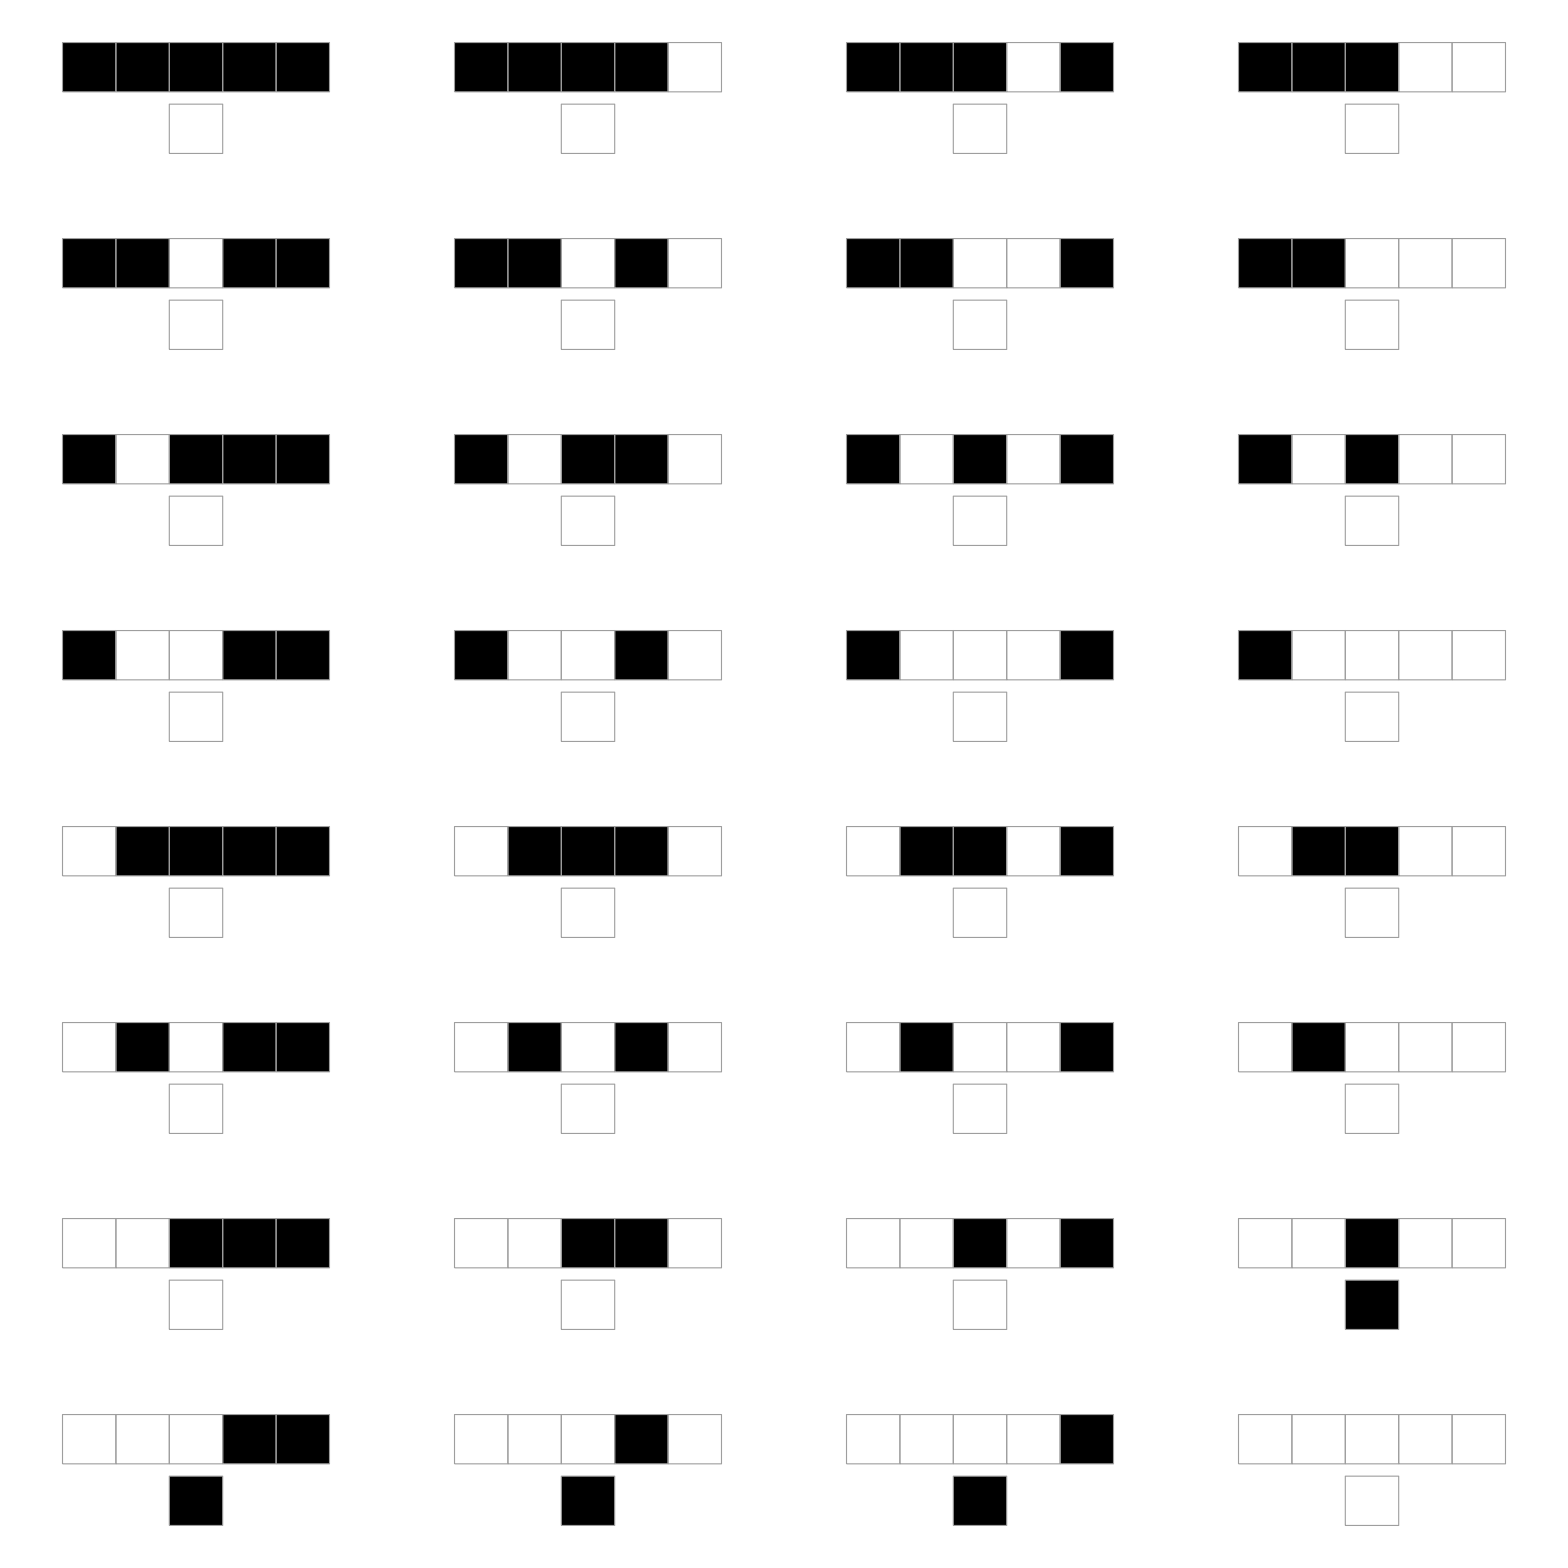

```mathematica
RulePlot[CellularAutomaton[{30,2,2}]]
```

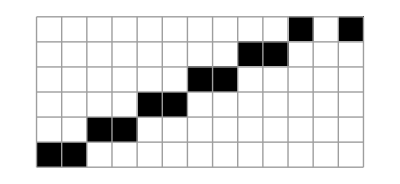

```mathematica
ArrayPlot[CellularAutomaton[{30,2,2},{{1,0,1},0},5],Mesh->All]
```

```mathematica
CellularAutomaton[{30,2,2},{{1},0},5]
```

{{0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,1,1,1},{0,0,0,0,0,0,1,1,0,0,0},{0,0,0,0,1,1,0,0,0,0,0},{0,0,1,1,0,0,0,0,0,0,0},{1,1,0,0,0,0,0,0,0,0,0}}

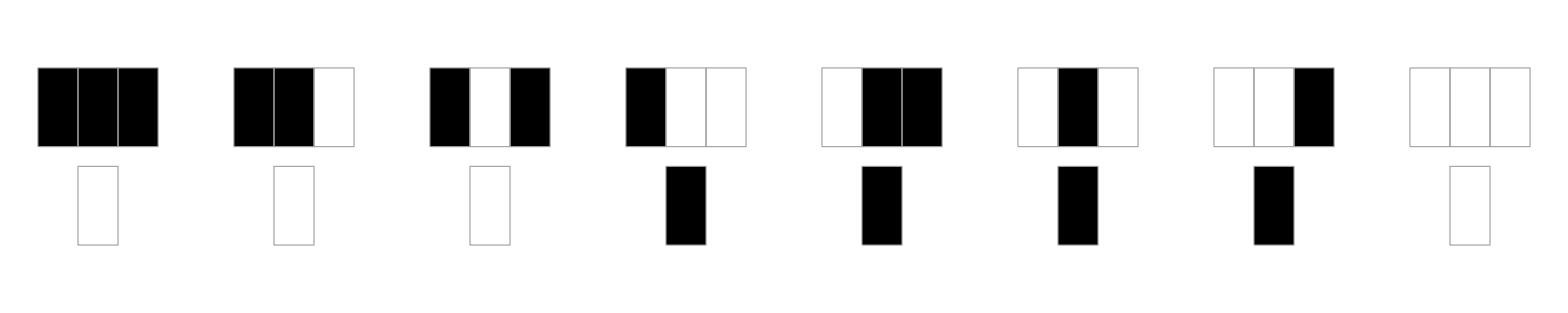

```mathematica
RulePlot[CellularAutomaton[{30,2,1}]]
```

```mathematica
Manipulate[ArrayPlot[CellularAutomaton[{i,2,1},{{1},0},100]],{i,1,255,1}]
```

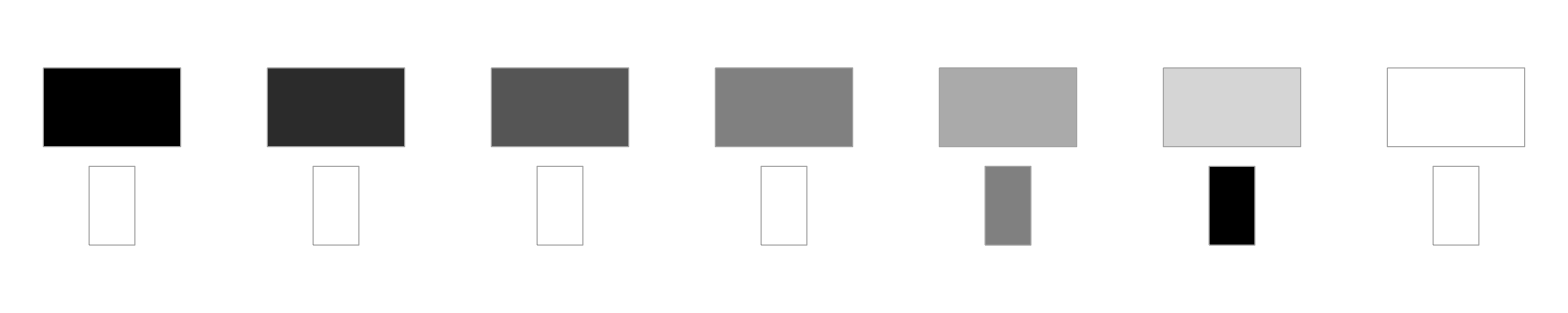

```mathematica
RulePlot[CellularAutomaton[{15,{3,1},1}]]
```

```mathematica
Manipulate[ArrayPlot[CellularAutomaton[{i,{3,1},1},{{1},0},100]],{i,1,255,1}]
```